(1.6039 (7999.72+x))/(√(-1.59989×10^7+(7999.72+x)^2))

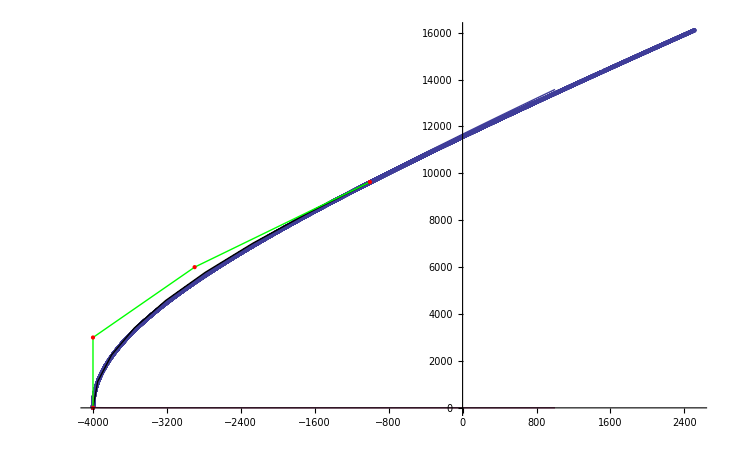

```mathematica
a=-4493.7147043875375;
b=-7207.450449550074;
e=Sqrt[1+b^2/a^2];
p=a(1-e);
f=1.05*b/a*Sqrt [(x+2*p)^2-p^2];
g = D[b/a*Sqrt [(x+2*p)^2-p^2],x]

firstPlot = Plot[{f,g},{x,-4000,1000}];
SetDirectory[NotebookDirectory[]];
data = Import["output.csv","Data"]//Short;
data2 = Import["output2.csv","Data"]//Short;
tableData = Table[data[[1]][[n]],{n,Length[data[[1]]]}];
tableData2 = Table[data2[[1]][[n]],{n,Length[data2[[1]]]}];

pts={{-4000,0},{-4000,3000},{-2900,6000},{-1003,9631}};
bezCurve = Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}];

Show[ListPlot[tableData],ListPlot[tableData2],firstPlot, bezCurve]
```

(1.6039 (7999.72+x))/(√(-1.59989×10^7+(7999.72+x)^2))

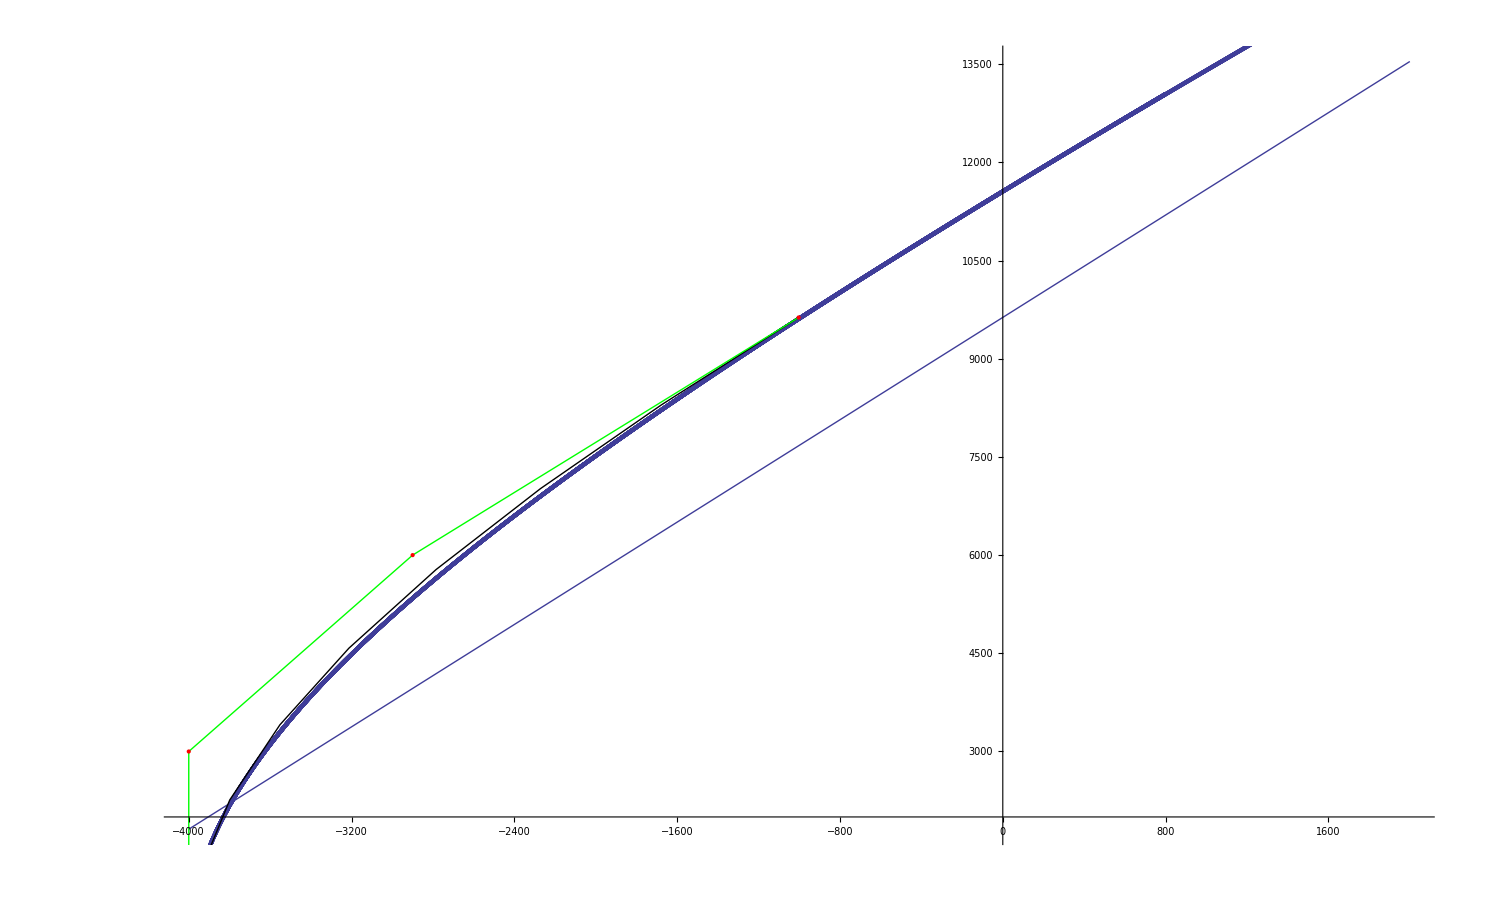

```mathematica
f=b/a*Sqrt [(x+2*p)^2-p^2];
g = D[b/a*Sqrt [(x+2*p)^2-p^2],x]
h=1.9546846142007634x+9631.701934852219;
j=105105115.86997849(x+4000);
gamma1=Plot[h,{x,-4000,2000}];
gamma2=Plot[j,{x,-4000,5000}];


Show[gamma1,gamma2,ListPlot[tableData],ListPlot[tableData2], bezCurve]
```